```mathematica
population=100000
```

100000

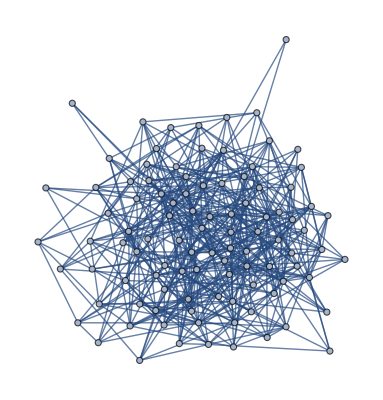

```mathematica
g=RandomGraph[{100,500}]
```

```mathematica
VertexList[g]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
i=RandomChoice[VertexList[g]]
```

10

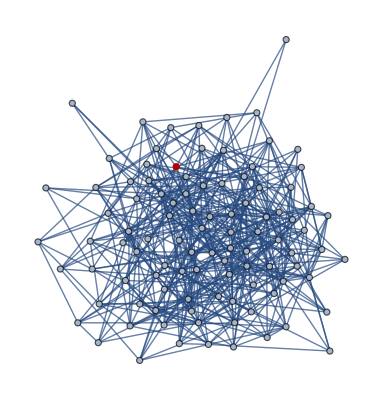

```mathematica
HighlightGraph[g,i]
```

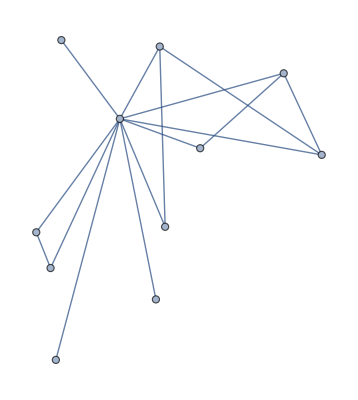

```mathematica
ng=NeighborhoodGraph[g,i]
```

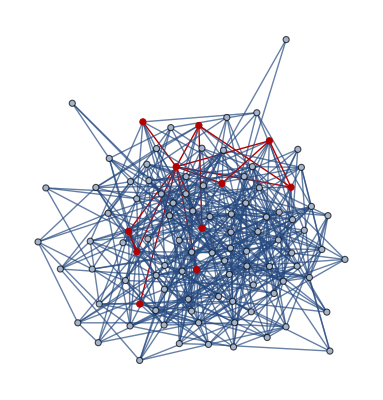

```mathematica
HighlightGraph[g,ng]
```

```mathematica
vl=VertexList[ng]
```

{10,6,13,37,56,62,67,79,84,88,93}

```mathematica
i2=Select[vl,RandomReal[]<0.25&]
```

{10,6,62,79,88}

```mathematica
i
```

10

```mathematica
i2=Complement[i2,{i}]
```

{6,62,79,88}

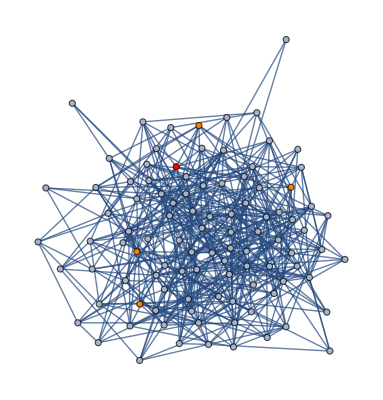

```mathematica
HighlightGraph[g,{Style[i,Red],Style[i2,Orange]}]
```